## Import data files and create interpolation objects

Native Coulomb wave form factors span the range E = 1 eV to 109.648 eV and:

outer valence Zeff=2*Sqrt[I / 13.6eV], where I = experimental ionisation energy:
for 5a1, q = 1 to 22.68 keV;
for 3e, q = 1 to 22.68 keV;
for 1a2, q = 1 to 22.68 keV;
(for 4e1, q = 1 to 22.68 keV; - here to test 4e2 accuracy)
for 4e2, q = 1 to 33.99 keV;
(for 5e1, q = 1 to 33.99 keV; - here to test 5e2 accuracy)
for 5e2, q = 1 to 33.99 keV;
for 6a, q = 1 to 38.89 keV.

inner valence Zeff=2*2*Sqrt[I / 13.6eV], where I = experimental ionisation energy:
for 3a1, q = 1 to 38.89 keV.
for 2e, q = 1 to 38.89 keV.
for 4a1, q = 1 to 38.89 keV.

core Zeff=2*Sqrt[I / 13.6eV], where I = PySCF ionisation energy (no experimental value):
for 1a1, q = 1 to 66.72 keV.
for 1e, q = 1 to 66.72 keV.
for 2a1, q = 1 to 66.72 keV.

q is the momentum transfer [in keV] and E is the electron kinetic energy [in keV].

For higher values of q than those above (where the form factor is very very small), we also give form factors where we match onto the (rescaled) plane wave results. The plots at the bottom of the notebook show this extrapolation.

### Coulomb wave

```mathematica
(*outer valence Zeff=1*)
SetDirectory[NotebookDirectory[]];
LC4H105a1grid=Import["C4H10_CW_5a1_grid.dat"];
LC4H103egrid=Import["C4H10_CW_3e2_grid.dat"];
LC4H104e1grid=Import["C4H10_CW_4e2_grid.dat"];
LC4H104e2grid=Import["C4H10_CW_4e2_grid.dat"];
LC4H101a2grid=Import["C4H10_CW_1a2_grid.dat"];
LC4H105e1grid=Import["C4H10_CW_5e2_grid.dat"];
LC4H105e2grid=Import["C4H10_CW_5e2_grid.dat"];
LC4H106a1grid=Import["C4H10_CW_6a1_grid.dat"];
ResetDirectory[];

fC4H105a1=Interpolation[LC4H105a1grid,InterpolationOrder->1]
fC4H103e=Interpolation[LC4H103egrid,InterpolationOrder->1]
fC4H104e1=Interpolation[LC4H104e1grid,InterpolationOrder->1]
fC4H104e2=Interpolation[LC4H104e2grid,InterpolationOrder->1]
fC4H101a2=Interpolation[LC4H101a2grid,InterpolationOrder->1]
fC4H105e1=Interpolation[LC4H105e2grid,InterpolationOrder->1]
fC4H105e2=Interpolation[LC4H105e2grid,InterpolationOrder->1]
fC4H106a1=Interpolation[LC4H106a1grid,InterpolationOrder->1]

(*inner valence Zeff=2.7*)
SetDirectory[NotebookDirectory[]];
LC4H103a1grid=Import["C4H10_CW_3a1_grid.dat"];
LC4H102egrid=Import["C4H10_CW_2e2_grid.dat"];
LC4H104a1grid=Import["C4H10_CW_4a1_grid.dat"];
ResetDirectory[];

fC4H103a1=Interpolation[LC4H103a1grid,InterpolationOrder->1]
fC4H102e=Interpolation[LC4H102egrid,InterpolationOrder->1]
fC4H104a1=Interpolation[LC4H104a1grid,InterpolationOrder->1]

(*core Zeff=4.7*)
SetDirectory[NotebookDirectory[]];
LC4H101a1grid=Import["C4H10_CW_1a1_grid.dat"];
LC4H101egrid=Import["C4H10_CW_1e2_grid.dat"];
LC4H102a1grid=Import["C4H10_CW_2a1_grid.dat"];
ResetDirectory[];

fC4H101a1=Interpolation[LC4H101a1grid,InterpolationOrder->1]
fC4H101e=Interpolation[LC4H101egrid,InterpolationOrder->1]
fC4H102a1=Interpolation[LC4H102a1grid,InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«11 more identical outputs»

### Coulomb wave + matched rescaled Plane wave at high q

```mathematica
(*outer valence*)
SetDirectory[NotebookDirectory[]];
LC4H10CWPW5a1grid=Import["C4H10_5a1_grid_PW_largeQ.dat"];
LC4H10CWPW3egrid=Import["C4H10_3e2_grid_PW_largeQ.dat"];
LC4H10CWPW4e1grid=Import["C4H10_4e2_grid_PW_largeQ.dat"];
LC4H10CWPW4e2grid=Import["C4H10_4e2_grid_PW_largeQ.dat"];
LC4H10CWPW1a2grid=Import["C4H10_1a2_grid_PW_largeQ.dat"];
LC4H10CWPW5e1grid=Import["C4H10_5e2_grid_PW_largeQ.dat"];
LC4H10CWPW5e2grid=Import["C4H10_5e2_grid_PW_largeQ.dat"];
LC4H10CWPW6a1grid=Import["C4H10_6a1_grid_PW_largeQ.dat"];
ResetDirectory[];

fC4H10CWPW5a1=Interpolation[LC4H10CWPW5a1grid,InterpolationOrder->1]
fC4H10CWPW3e=Interpolation[LC4H10CWPW3egrid,InterpolationOrder->1]
fC4H10CWPW4e1=Interpolation[LC4H10CWPW4e1grid,InterpolationOrder->1]
fC4H10CWPW4e2=Interpolation[LC4H10CWPW4e2grid,InterpolationOrder->1]
fC4H10CWPW1a2=Interpolation[LC4H10CWPW1a2grid,InterpolationOrder->1]
fC4H10CWPW5e1=Interpolation[LC4H10CWPW5e1grid,InterpolationOrder->1]
fC4H10CWPW5e2=Interpolation[LC4H10CWPW5e2grid,InterpolationOrder->1]
fC4H10CWPW6a1=Interpolation[LC4H10CWPW6a1grid,InterpolationOrder->1]

(*inner valence*)
SetDirectory[NotebookDirectory[]];
LC4H10CWPW3a1grid=Import["C4H10_3a1_grid_PW_largeQ.dat"];
LC4H10CWPW2egrid=Import["C4H10_2e2_grid_PW_largeQ.dat"];
LC4H10CWPW4a1grid=Import["C4H10_4a1_grid_PW_largeQ.dat"];
ResetDirectory[];

fC4H10CWPW3a1=Interpolation[LC4H10CWPW3a1grid,InterpolationOrder->1]
fC4H10CWPW2e=Interpolation[LC4H10CWPW2egrid,InterpolationOrder->1]
fC4H10CWPW4a1=Interpolation[LC4H10CWPW4a1grid,InterpolationOrder->1]

(*core*)
SetDirectory[NotebookDirectory[]];
LC4H10CWPW1a1grid=Import["C4H10_1a1_grid_PW_largeQ.dat"];
LC4H10CWPW1egrid=Import["C4H10_1e2_grid_PW_largeQ.dat"];
LC4H10CWPW2a1grid=Import["C4H10_2a1_grid_PW_largeQ.dat"];
ResetDirectory[];

fC4H10CWPW1a1=Interpolation[LC4H10CWPW1a1grid,InterpolationOrder->1]
fC4H10CWPW1e=Interpolation[LC4H10CWPW1egrid,InterpolationOrder->1]
fC4H10CWPW2a1=Interpolation[LC4H10CWPW2a1grid,InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«11 more identical outputs»

### Plots

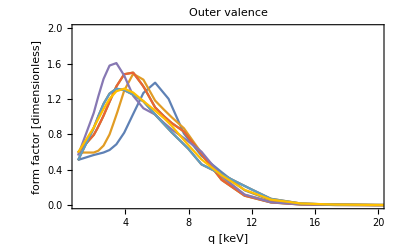

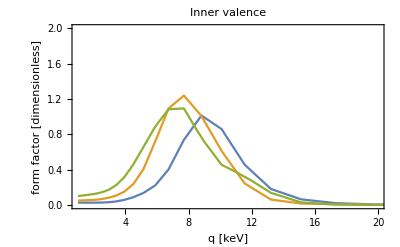

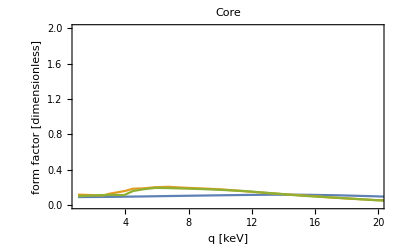

```mathematica
EtestkeV=0.025;

Plot[{fC4H105a1[q,EtestkeV],fC4H103e[q,EtestkeV],fC4H104e1[q,EtestkeV],fC4H104e2[q,EtestkeV],fC4H101a2[q,EtestkeV],fC4H105e1[q,EtestkeV],fC4H105e2[q,EtestkeV],fC4H106a1[q,EtestkeV]},{q,1,50},PlotRange->{{1,20},{0,2}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotLabel->"Outer valence"]

Plot[{fC4H103a1[q,EtestkeV],fC4H102e[q,EtestkeV],fC4H104a1[q,EtestkeV]},{q,1,50},PlotRange->{{1,20},{0,2}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotLabel->"Inner valence"]

Plot[{fC4H101a1[q,EtestkeV],fC4H101e[q,EtestkeV],fC4H102a1[q,EtestkeV]},{q,1,50},PlotRange->{{1,20},{0,2}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotLabel->"Core"]
```

### Plots - showing the plane wave extrapolation in black

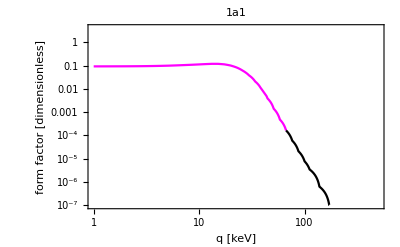

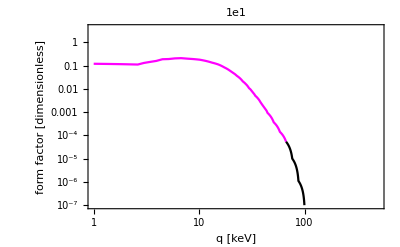

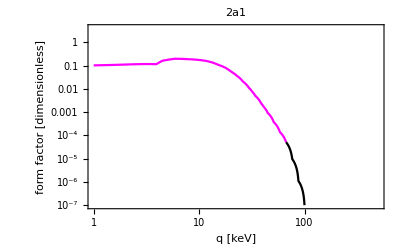

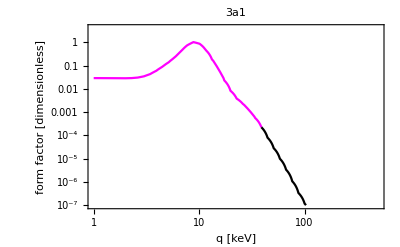

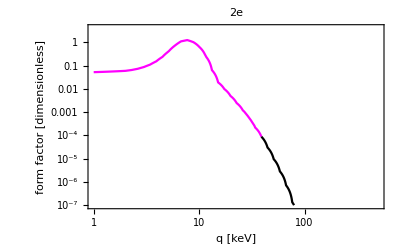

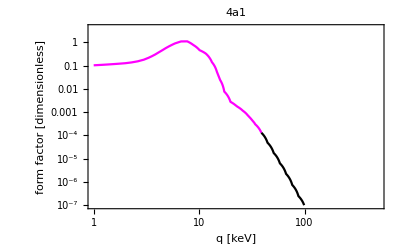

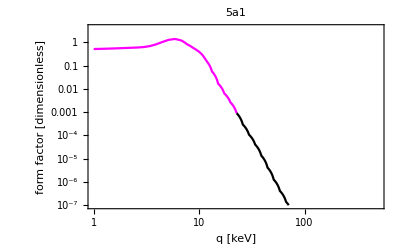

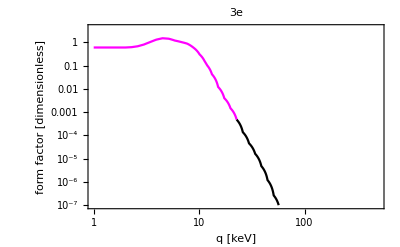

```mathematica
EtestkeV=0.025;

Show[LogLogPlot[{fC4H101a1[q,EtestkeV]},{q,1,LC4H101a1grid[[-1,1]]},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->Magenta],LogLogPlot[{fC4H10CWPW1a1[q,EtestkeV]},{q,LC4H101a1grid[[-1,1]],200},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->{Black}],PlotLabel->"1a1"]

Show[LogLogPlot[{fC4H101e[q,EtestkeV]},{q,1,LC4H101egrid[[-1,1]]},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->Magenta],LogLogPlot[{fC4H10CWPW1e[q,EtestkeV]},{q,LC4H101egrid[[-1,1]],200},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->{Black}],PlotLabel->"1e1"]

Show[LogLogPlot[{fC4H102a1[q,EtestkeV]},{q,1,LC4H102a1grid[[-1,1]]},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->Magenta],LogLogPlot[{fC4H10CWPW2a1[q,EtestkeV]},{q,LC4H102a1grid[[-1,1]],200},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->{Black}],PlotLabel->"2a1"]

Show[LogLogPlot[{fC4H103a1[q,EtestkeV]},{q,1,LC4H103a1grid[[-1,1]]},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->Magenta],LogLogPlot[{fC4H10CWPW3a1[q,EtestkeV]},{q,LC4H103a1grid[[-1,1]],200},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->{Black}],PlotLabel->"3a1"]

Show[LogLogPlot[{fC4H102e[q,EtestkeV]},{q,1,LC4H102egrid[[-1,1]]},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->Magenta],LogLogPlot[{fC4H10CWPW2e[q,EtestkeV]},{q,LC4H102egrid[[-1,1]],200},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->{Black}],PlotLabel->"2e"]


Show[LogLogPlot[{fC4H104a1[q,EtestkeV]},{q,1,LC4H104a1grid[[-1,1]]},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->Magenta],LogLogPlot[{fC4H10CWPW4a1[q,EtestkeV]},{q,LC4H104a1grid[[-1,1]],200},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->{Black}],PlotLabel->"4a1"]

Show[LogLogPlot[{fC4H105a1[q,EtestkeV]},{q,1,LC4H105a1grid[[-1,1]]},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->Magenta],LogLogPlot[{fC4H10CWPW5a1[q,EtestkeV]},{q,LC4H105a1grid[[-1,1]],200},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->{Black}],PlotLabel->"5a1"]

Show[LogLogPlot[{fC4H103e[q,EtestkeV]},{q,1,LC4H103egrid[[-1,1]]},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->Magenta],LogLogPlot[{fC4H10CWPW3e[q,EtestkeV]},{q,LC4H103egrid[[-1,1]],200},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->{Black}],PlotLabel->"3e"]


Show[LogLogPlot[{fC4H101a2[q,EtestkeV]},{q,1,LC4H101a2grid[[-1,1]]},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->Magenta],LogLogPlot[{fC4H10CWPW1a2[q,EtestkeV]},{q,LC4H101a2grid[[-1,1]],200},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->{Black}],PlotLabel->"1a2"]

Show[LogLogPlot[{fC4H104e1[q,EtestkeV]},{q,1,LC4H104e1grid[[-1,1]]},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->Magenta],LogLogPlot[{fC4H10CWPW4e1[q,EtestkeV]},{q,LC4H104e1grid[[-1,1]],200},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->{Black}],PlotLabel->"4e1"]

Show[LogLogPlot[{fC4H104e2[q,EtestkeV]},{q,1,LC4H104e2grid[[-1,1]]},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->Magenta],LogLogPlot[{fC4H10CWPW4e2[q,EtestkeV]},{q,LC4H104e2grid[[-1,1]],200},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->{Black}],PlotLabel->"4e2"]

Show[LogLogPlot[{fC4H105e1[q,EtestkeV]},{q,1,LC4H105e1grid[[-1,1]]},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->Magenta],LogLogPlot[{fC4H10CWPW5e1[q,EtestkeV]},{q,LC4H105e1grid[[-1,1]],200},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->{Black}],PlotLabel->"5e1"]

Show[LogLogPlot[{fC4H105e2[q,EtestkeV]},{q,1,LC4H105e2grid[[-1,1]]},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->Magenta],LogLogPlot[{fC4H10CWPW5e2[q,EtestkeV]},{q,LC4H105e2grid[[-1,1]],200},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->{Black}],PlotLabel->"5e2"]


Show[LogLogPlot[{fC4H106a1[q,EtestkeV]},{q,1,LC4H106a1grid[[-1,1]]},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->Magenta],LogLogPlot[{fC4H10CWPW6a1[q,EtestkeV]},{q,LC4H106a1grid[[-1,1]],200},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->{Black}],PlotLabel->"6a1"]
```